```mathematica
f1[x_] := x - 1/2
```

```mathematica
f1[1]
```

1/2

```mathematica
f2[x_]:= (x/2) - 1/4
```

```mathematica
f2[1]
```

1/4

```mathematica
Expand[f1(x)]
```

f1 x

```mathematica
?f1
```

Global`f1

f1[x_]:=x-1/2

```mathematica
f1[(1 + a)]
```

1/2+a

```mathematica
Expand[f[x]
```

```mathematica
]
```

```mathematica
Expand[f1[x]]
```

-1/2+x

```mathematica
x
```

x

```mathematica
1+2x/.x->3
```

7

```mathematica
x
```

x

```mathematica
eb[x_,n_]:=Exp[-i2πnx]
```

```mathematica
eb[3,2]
```

ⅇ^-i2πnx

```mathematica
eb[x_,n_]:=Exp[-i2πnx]
```

```mathematica
clear[eb]
```

clear[eb]

```mathematica
eb
```

eb

```mathematica
?eb
```

Global`eb

eb[x_,n_]:=Exp[-i2πnx]

```mathematica
Clear[eb]
```

```mathematica
?eb
f1
```

Global`eb

f1

```mathematica
?f2
```

Global`f2

f2[x_]:=x/2-1/4

```mathematica
?f1
```

Global`f1

f1[x_]:=x-1/2

```mathematica
eb[n_,x_]:=Exp[-i2πnx]
```

```mathematica
eb[4,5]
```

ⅇ^-i2πnx

```mathematica
f1[2]
```

3/2

```mathematica
eb[{2,3}]
```

eb[{2,3}]

```mathematica
Clear[eb]
```

```mathematica
b[y_,x_] := Exp[-i2πyx]
```

```mathematica
b[2,5]
```

ⅇ^-i2πyx

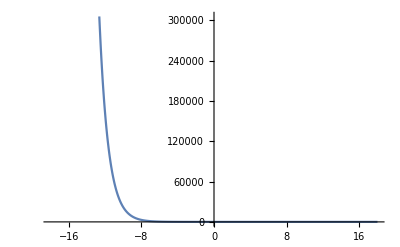

```mathematica
Plot[ⅇ^-i2πnx,{i2πnx,-18.,18.}]
```

```mathematica
f[x_,y_]:=(y/x)+x*y
```

```mathematica
f[1,2]
```

4

```mathematica
Clear[f]
```

```mathematica
?b
```

Global`b

b[y_,x_]:=Exp[-i2πyx]

```mathematica
Clear[b]
```

```mathematica
?b
"
```

Global`b

```mathematica
?b
```

Global`b

```mathematica
?b
```

Global`b

```mathematica
?f1
```

Global`f1

f1[x_]:=x-1/2

```mathematica
b[x_,y_]=x + y
```

x+y

```mathematica
b[1,2]
```

3

```mathematica
Clear[b]
```

```mathematica
b[n_,x_] := 3n + x
```

```mathematica
b[3,2]
```

11

```mathematica
Clear[b]
```

```mathematica
b[n_,x_] := Exp[nx]
```

```mathematica
b[2,1]
```

ⅇ^nx

```mathematica
Clear[b]
```

```mathematica
?b
```

Global`b

```mathematica
b[3]
```

ⅇ^9

```mathematica
Integral[b[x],{x,0,1}]
```

Integral[ⅇ^(3 x),{x,0,1}]

```mathematica
?b
```

Global`b

```mathematica
e^3
```

e^3

```mathematica
x^4
```

x^4

```mathematica
ϵ^3
```

```mathematica
\
```

```mathematica
Plot[ϵ^3,{ϵ,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
\[E]
```

```mathematica
\[e]
```

```mathematica
?e
```

Global`e

```mathematica
E
```

ⅇ

```mathematica
E^4
```

ⅇ^4

```mathematica
N[ⅇ^4]
```

54.5982

```mathematica
N[E^3]
```

20.0855

```mathematica
?b
```

Global`b

```mathematica
b[n_,x_] := E^i2πnx
```

```mathematica
b[4,2]
```

ⅇ^i2πnx

```mathematica
N[b[2,1]]
```

2.71828^i2πnx

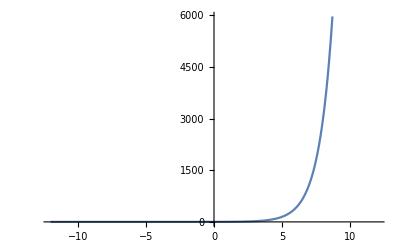

```mathematica
Plot[2.718281828459045^i2πnx,{i2πnx,-12.,12.}]
```

```mathematica
Clear[b]
```

```mathematica
b[n_,x_] := E^(i 2π n x)
```

```mathematica
b[3,2]
```

ⅇ^(12 i π)

```mathematica
N[b[2,1]
```

```mathematica
]
```

```mathematica
N[b[2,1]]
```

```mathematica
TeXForm[2.718281828459045^(12.566370614359172 i)]
```

2.71828^{12.5664 i}

```mathematica
ToExpression["b[1,2]",TeXForm]
```

ⅇ^(4 i π)

```mathematica
Integrate[f1[x] b[n,x],{x,0,1}]
```

```mathematica
N[(1 + i*n*Pi + E^(2*i*n*Pi)*(-1 + i*n*Pi))/(4*i^2*n^2*Pi^2)/.n->1]
```

(0.0253303 (1.+3.14159 i+2.71828^(6.28319 i) (-1.+3.14159 i)))/i^2

```mathematica
Series[(1 + i*n*Pi + E^(2*i*n*Pi)*(-1 + i*n*Pi))/(4*i^2*n^2*Pi^2),{n,0,10}]
```

(i π n)/6+1/6 i^2 π^2 n^2+1/10 i^3 π^3 n^3+2/45 i^4 π^4 n^4+1/63 i^5 π^5 n^5+1/210 i^6 π^6 n^6+1/810 i^7 π^7 n^7+(4 i^8 π^8 n^8)/14175+(i^9 π^9 n^9)/17325+(i^10 π^10 n^10)/93555+O[n]^11

```mathematica
TeXForm[Integrate[f2[x] b[n,x],x]]
```

```mathematica
TeXForm[Integrate[f2[x] b[n, x], x]]TeXForm[Integrate[f2[x] b[n, x], x]]TeXForm[Integrate[f2[x] b[n, x], x]
Integrate[3 b[n,x], x]
```

(3*E^(2*i*n*Pi*x))/(2*i*n*Pi)

```mathematica
Series[x,{x,10,20}]
```

10+(x-10)+O[x-10]^21

```mathematica
n
```

```mathematica
Abs[(1 + i*n*Pi + E^(2*i*n*Pi)*(-1 + i*n*Pi))/(4*i^2*n^2*Pi^2)/.n->1]
```

Abs[(1+i π+ⅇ^(2 i π) (-1+i π))/i^2]/(4 π^2)

```mathematica
(1 + i*n*Pi + E^(2*i*n*Pi)*(-1 + i*n*Pi))/(4*i^2*n^2*Pi^2)/.n->1
```

```mathematica
(1+ⅈ π+ⅇ^(2 ⅈ π) (-1+ⅈ π))/(4 ⅈ^2 π^2)
```

-ⅈ/(2 π)